## Para un n fija

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
Res=1*10^(-8);
```

### Datos experimentales

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=-n *SphericalBesselJ[n,ρ]+ ρ * SphericalBesselJ[n-1,ρ] 
dξn[n_,ρ_]:=-n * SphericalHankelH1[n,ρ] + ρ* SphericalHankelH1[n-1,ρ]
```

nm : índice de refracción del medio
a : radio de la partícula
ω : frecuencia angular
ωp : frecuencia de plasma
γ : constante de amortiguamiento

nm = 1, A = a ωp/c , W= ω/ ωp, G= γ/ωp = 10^-2

```mathematica
nm=1;
G= 10*^-2;
```

```mathematica
mieSeccTrans[A_,W_,n_]:=Module[{np,m,x,an,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x]));
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[an]^2+Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[an+ bn]);

{an,bn,Qsca,Qext}]
```

## Cálculos

### Modelo de Drude

#### Para ℏω = 13.142 eV, ℏγ = 0.197 eV y a = 60 nm

```mathematica
result1=Table[{(2 Pi c/W/(13.142/ℏ)),mieSeccTrans[#,W,1][[4]]},{W,0.2097,1.888145,0.001}]&/@{5*(13.142/ℏ)/c,10*(13.142/ℏ)/c,20*(13.142/ℏ)/c,30*(13.142/ℏ)/c,40*(13.142/ℏ)/c,50*(13.142/ℏ)/c};
```

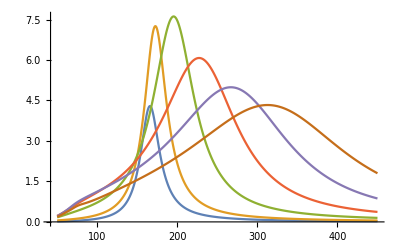

```mathematica
ListLinePlot[result1,AxesLabel->{"",""},PlotRange->All]
```

```mathematica
120*(13.142/ℏ)/c
```

7.98649

```mathematica
1*(13.142/ℏ)/c
```

0.066554

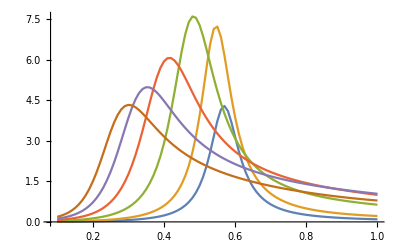

```mathematica
result2=Table[{W,mieSeccTrans[#,W,1][[4]]},{W,0.1,1,0.01}]&/@{5*(13.142/ℏ)/c,10*(13.142/ℏ)/c,20*(13.142/ℏ)/c,30*(13.142/ℏ)/c,40*(13.142/ℏ)/c,50*(13.142/ℏ)/c};
ListLinePlot[result2,AxesLabel->{"",""},PlotRange->All]
```

```mathematica
2.3*(13.142/ℏ)/c
2.3*(13.142/ℏ)/c
```

0.153074

0.153074

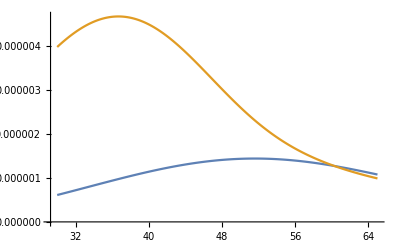

```mathematica
result3=Table[{W,mieSeccTrans[#,W,4][[4]]},{W,30,65,0.01}]&/@{1.6*(13.142/ℏ)/c,2.3*(13.142/ℏ)/c};
ListLinePlot[result3,AxesLabel->{"",""},PlotRange->All]
```

```mathematica
Table[{anc,GoldenSearchMax[anc,35,55,4]},{anc,0.1,0.16,0.01}]
```

```mathematica
GoldenSearchMax[0.1,35,55,4]
```

54.7532

```mathematica
GoldenSearchMax[anc_,lower_,upper_,n_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[mieSeccTrans[anc,c,n][[4]]>mieSeccTrans[anc,d,n][[4]],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Return[(b+a)/2]];
```

```mathematica
ω1=Table[{anc,GoldenSearchMax[anc,0.1,1,1]},{anc,0.1,8,0.01}];
```

$Aborted

```mathematica
ω2=Table[{anc,GoldenSearchMax[anc,0.1,1,2]},{anc,0.1,8,0.01}];
```

$Aborted

$Aborted

```mathematica
ω3=Table[{anc,GoldenSearchMax[anc,0.1,1,3]},{anc,0.1,8,0.01}];
```

$Aborted

$Aborted

$Aborted

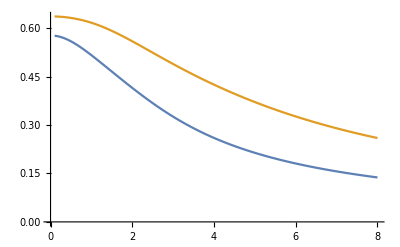

```mathematica
ListLinePlot[{ω1,ω2},PlotRange->All]
```

```mathematica
(*
```